Coded by Manish J. Thapa under supervision of Dr. Johannes Heinsoo @Quantum Device Lab, ETH Zurich, April 2016

```mathematica
colorscheme1=Table[Blend[{Red,White,Blue},i^2],{i,0,1,0.1}];
```

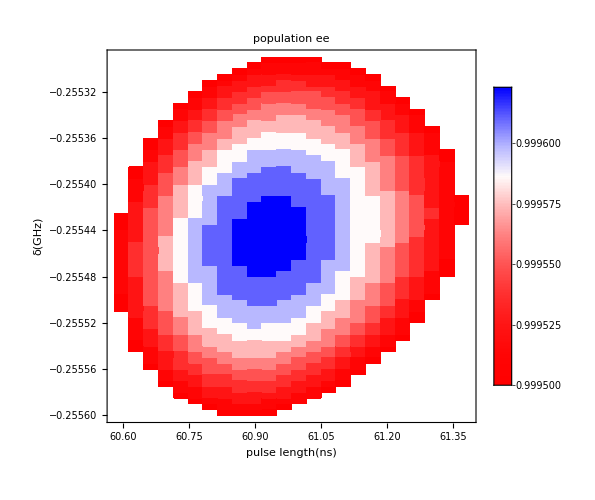

```mathematica
ListDensityPlot[Import["smoothlandfid.dat"],Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],ColorFunction->colorscheme1,PlotRange->{All,All,{0.9995,1}},DataRange->{{59,63},{-0.257,-0.253}},PerformanceGoal->"Quality",FrameLabel->{"pulse length(ns)","δ(GHz)"},LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"population ee",InterpolationOrder->0]
```

```mathematica
(*{{59,63},{-0.257,-0.253},sigma=1.7857 ns*)
```

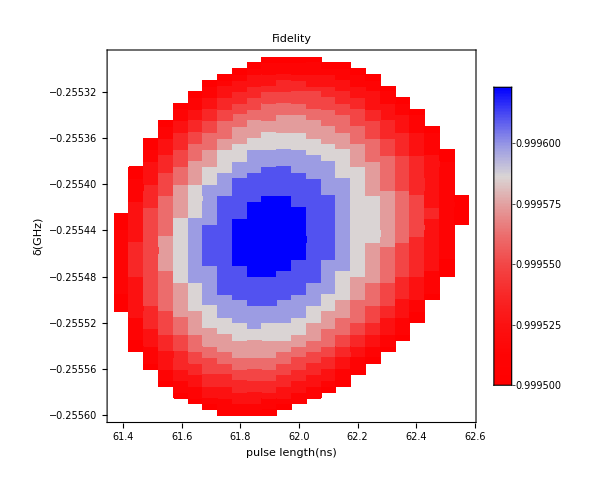

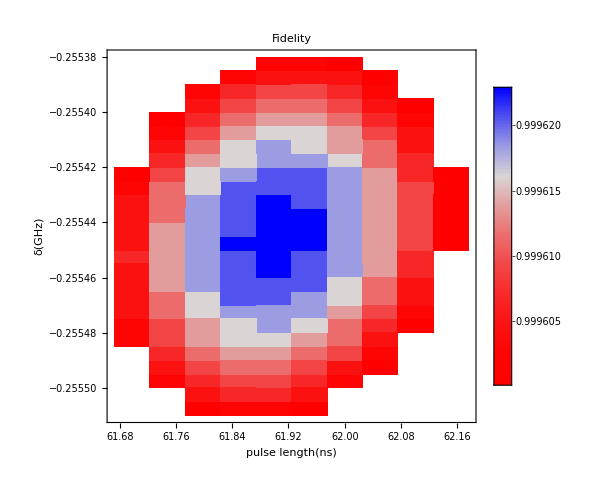

```mathematica
LastOrEmpty[seq_]:=If[Length[seq]>0,Last[seq],{}];

(*AddLabel[lab_,pos_]:=Inset[Framed[lab,Background->White,FrameStyle->None],pos];*)
AddLabel[lab_,pos_]:=Inset[Framed[Style[lab,18],Background->None,FrameStyle->None],pos];
AddLines[xs_,ys_,xlvl_,ylvl_]:={GridLines->{LastOrEmpty/@xs,LastOrEmpty/@ys},Epilog->Join[Table[AddLabel[xs[[i,1]],{xs[[i,2]],ylvl}],{i,Length[xs]}],Table[AddLabel[ys[[i,1]],{xlvl,ys[[i,2]]}],{i,Length[ys]}]]};
```

```mathematica
colorschememan=Table[Blend[{ColorData[104,"ColorList"][[5]],ColorData[13,"ColorList"][[2]]},i^2],{i,0,1,0.1}];
```

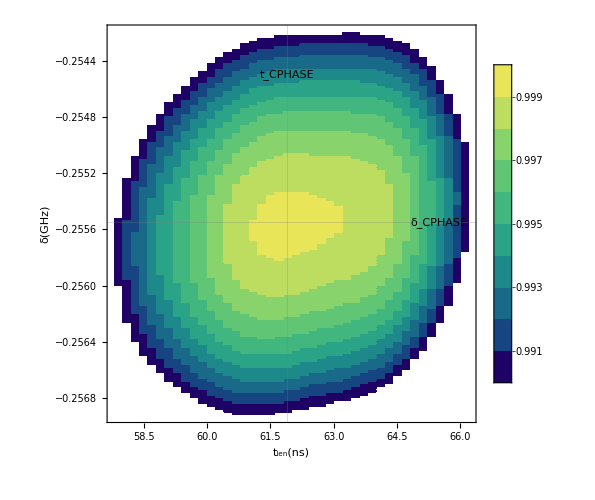

```mathematica
p4=ListContourPlot[Import["new_fid_26525000002_53_73_02_x.dat"],Mesh->None,ImageSize->500,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->430,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->10,FontFamily->"Helvetica"}],Right],PlotRange->{All,All,{0.99,1}},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"t_len(ns)","δ(GHz)"},TicksStyle->Directive[Orange,10],LabelStyle->Directive[FontSize->11,FontFamily->"Helvetica"],ImageSize->500,InterpolationOrder->0,ColorFunction->"BlueGreenYellow",AddLines[{Subscript[t,CPHASE]->61.9},{Subscript[δ,CPHASE]->-0.25555},65.5,-0.2545],Method->{"GridLinesInFront"->True}]
```

```mathematica
Export["densityplotFid.png",p4]
```

densityplotFid.png

```mathematica
p5=ListContourPlot[Import["new_fid_26525000002_53_73_02_x.dat"],Mesh->None,ImageSize->500,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->357,LegendMargins->{{0,0},{10,8}},LabelStyle->Directive[Black,22]],Right],PlotRange->{All,All,{0.99,1}},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"t_len(ns)","δ(GHz)"},TicksStyle->Directive[Orange,10],LabelStyle->Directive[Black,22],ImageSize->500,InterpolationOrder->0,ColorFunction->"BlueGreenYellow",AddLines[{Subscript[t,CPHASE]->61.9},{Subscript[δ,CPHASE]->-0.25555},65.5,-0.2545],Method->{"GridLinesInFront"->True}]
```

-Graphics-

```mathematica
Export["newdensityplotFid.png",p5]
```

newdensityplotFid.png